```mathematica
suit ={"A",2,3,4,5,6,7,8,9,10,"J","Q","K"};
myDeck = Join[suit, suit, suit, suit];
myDeck = {#}&/@myDeck;
myDeck = myDeck/.{"J"->10,"Q"->10,"K"->10, {"A"}->{1, 11}};
```

```mathematica
deck
```

{{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10}}

```mathematica
twoCards = Subsets[deck,{2}];
```

```mathematica
twoCards[[1]]
```

{{1,11},{2}}

```mathematica
enumeratedAces = Tuples/@twoCards;
```

```mathematica
enumeratedTotal = Total[#,{2}]&/@enumeratedAces;
```

```mathematica
under21 = Select[#, #<=21&]&/@enumeratedTotal;
```

```mathematica
finalScore = Max/@under21;
```

```mathematica
Length[finalScore]
```

325

```mathematica
Count[finalScore, {}]
```

0

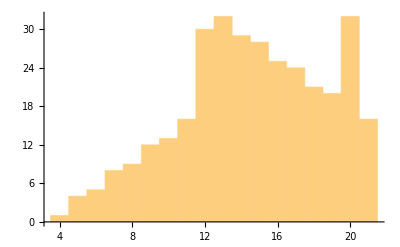

```mathematica
Histogram[finalScore]
```

```mathematica
drawCards[deck_,n_]:= Total[#,{2}]&/@(Tuples/@Subsets[deck,{n}])

bustCards[cards_, limit_]:=Max/@(Select[#, #<=limit&]&/@ cards)

regFail [cards_,minNeeded_,limit_]:=Count[bustCards[cards, limit],x_/;-1<x<minNeeded]/Length[cards]

regSuccess [cards_,minNeeded_,limit_]:=Count[bustCards[cards, limit],x_/;minNeeded<=x<limit]/Length[cards]

critFail [cards_,minNeeded_,limit_]:=
Count[bustCards[cards, limit],x_/;x<0]/Length[cards]

critSuccess[cards_,minNeeded_,limit_]:=Count[bustCards[cards, limit],limit]/Length[cards]

successVector[cards_,minNeeded_, limit_]:=
N[#,3]&/@{minNeeded - 1,
1-((minNeeded-2)*0.05),
minNeeded,
regSuccess[cards, minNeeded, limit]+critSuccess[cards, minNeeded, limit],
regFail[cards, minNeeded, limit]+critFail[cards, minNeeded, limit],
critSuccess[cards, minNeeded, limit],
critFail[cards, minNeeded, limit],
regSuccess[cards, minNeeded, limit],
regFail[cards, minNeeded, limit]
}

bustOdds [list_]:=N[Count[list,-∞]/Length[list]]
```

```mathematica
drawTwo = drawCards[myDeck,2];
drawThree = drawCards[myDeck,3];
drawFour = drawCards[myDeck, 4];
drawFive = drawCards[myDeck, 5];
drawSix = drawCards[myDeck,6];
```

```mathematica
headings = {"Min. Roll","Roll Success","Min. Needed","Tot. Success","Tot. Fail","Crit. Success","Crit. Fail","Reg. Success", "Reg. Fail"};
```

```mathematica
Grid[Prepend[Table[successVector[drawTwo,n,21],{n,2,21}],headings],
{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}}]
```

Min. Roll | Roll Success | Min. Needed | Tot. Success | Tot. Fail | Crit. Success | Crit. Fail | Reg. Success | Reg. Fail
1. | 1. | 2. | 1. | 0 | 0.0483 | 0 | 0.952 | 0
2. | 0.95 | 3. | 1. | 0 | 0.0483 | 0 | 0.952 | 0
3. | 0.9 | 4. | 1. | 0 | 0.0483 | 0 | 0.952 | 0
4. | 0.85 | 5. | 0.995 | 0.00452 | 0.0483 | 0 | 0.947 | 0.00452
5. | 0.8 | 6. | 0.983 | 0.0166 | 0.0483 | 0 | 0.935 | 0.0166
6. | 0.75 | 7. | 0.967 | 0.0332 | 0.0483 | 0 | 0.919 | 0.0332
7. | 0.7 | 8. | 0.943 | 0.0573 | 0.0483 | 0 | 0.894 | 0.0573
8. | 0.65 | 9. | 0.914 | 0.086 | 0.0483 | 0 | 0.866 | 0.086
9. | 0.6 | 10. | 0.878 | 0.122 | 0.0483 | 0 | 0.83 | 0.122
10. | 0.55 | 11. | 0.837 | 0.163 | 0.0483 | 0 | 0.789 | 0.163
11. | 0.5 | 12. | 0.789 | 0.211 | 0.0483 | 0 | 0.741 | 0.211
12. | 0.45 | 13. | 0.695 | 0.305 | 0.0483 | 0 | 0.647 | 0.305
13. | 0.4 | 14. | 0.599 | 0.401 | 0.0483 | 0 | 0.551 | 0.401
14. | 0.35 | 15. | 0.51 | 0.49 | 0.0483 | 0 | 0.462 | 0.49
15. | 0.3 | 16. | 0.425 | 0.575 | 0.0483 | 0 | 0.377 | 0.575
16. | 0.25 | 17. | 0.348 | 0.652 | 0.0483 | 0 | 0.3 | 0.652
17. | 0.2 | 18. | 0.276 | 0.724 | 0.0483 | 0 | 0.228 | 0.724
18. | 0.15 | 19. | 0.211 | 0.789 | 0.0483 | 0 | 0.163 | 0.789
19. | 0.1 | 20. | 0.151 | 0.849 | 0.0483 | 0 | 0.103 | 0.849
20. | 0.05 | 21. | 0.0483 | 0.952 | 0.0483 | 0 | 0 | 0.952

```mathematica
Grid[Prepend[Table[successVector[drawThree,n,21],{n,2,21}],headings],
{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}}]
```

Min. Number | Tot. Success | Tot. Fail | Crit. Success | Crit. Fail | Reg. Success | Reg. Fail
2. | 0.622 | 0.378 | 0.091 | 0.378 | 0.531 | 0
3. | 0.622 | 0.378 | 0.091 | 0.378 | 0.531 | 0
4. | 0.622 | 0.378 | 0.091 | 0.378 | 0.531 | 0
5. | 0.622 | 0.378 | 0.091 | 0.378 | 0.531 | 0
6. | 0.622 | 0.378 | 0.091 | 0.378 | 0.531 | 0
7. | 0.622 | 0.378 | 0.091 | 0.378 | 0.53 | 0.000181
8. | 0.62 | 0.38 | 0.091 | 0.378 | 0.529 | 0.00127
9. | 0.618 | 0.382 | 0.091 | 0.378 | 0.527 | 0.00344
10. | 0.614 | 0.386 | 0.091 | 0.378 | 0.523 | 0.0076
11. | 0.608 | 0.392 | 0.091 | 0.378 | 0.517 | 0.0138
12. | 0.599 | 0.401 | 0.091 | 0.378 | 0.508 | 0.0228
13. | 0.571 | 0.429 | 0.091 | 0.378 | 0.48 | 0.0509
14. | 0.533 | 0.467 | 0.091 | 0.378 | 0.442 | 0.0883
15. | 0.489 | 0.511 | 0.091 | 0.378 | 0.398 | 0.133
16. | 0.436 | 0.564 | 0.091 | 0.378 | 0.345 | 0.186
17. | 0.377 | 0.623 | 0.091 | 0.378 | 0.286 | 0.245
18. | 0.311 | 0.689 | 0.091 | 0.378 | 0.22 | 0.31
19. | 0.242 | 0.758 | 0.091 | 0.378 | 0.151 | 0.38
20. | 0.167 | 0.833 | 0.091 | 0.378 | 0.0764 | 0.454
21. | 0.091 | 0.909 | 0.091 | 0.378 | 0 | 0.531

```mathematica
Grid[Prepend[Table[successVector[drawFour,n,21],{n,2,21}],headings],
{Background->{None,{{White,Lighter[Blend[{Blue,Green}],0.8]}}},Dividers->{{Gray,{LightGray},Gray}},Frame->True,Spacings->{2,{2,{0.7},2}}}]
```

Min. Number | Tot. Success | Tot. Fail | Crit. Success | Crit. Fail | Reg. Success | Reg. Fail
2. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0
3. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0
4. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0
5. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0
6. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0
7. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0
8. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0
9. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 3.69×10^-6
10. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.181 | 0.0000628
11. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.18 | 0.000255
12. | 0.226 | 0.774 | 0.0457 | 0.774 | 0.18 | 0.000728
13. | 0.22 | 0.78 | 0.0457 | 0.774 | 0.175 | 0.00584
14. | 0.213 | 0.787 | 0.0457 | 0.774 | 0.168 | 0.013
15. | 0.203 | 0.797 | 0.0457 | 0.774 | 0.157 | 0.0233
16. | 0.189 | 0.811 | 0.0457 | 0.774 | 0.144 | 0.037
17. | 0.171 | 0.829 | 0.0457 | 0.774 | 0.125 | 0.0553
18. | 0.148 | 0.852 | 0.0457 | 0.774 | 0.102 | 0.0782
19. | 0.12 | 0.88 | 0.0457 | 0.774 | 0.074 | 0.107
20. | 0.0858 | 0.914 | 0.0457 | 0.774 | 0.04 | 0.141
21. | 0.0457 | 0.954 | 0.0457 | 0.774 | 0 | 0.181

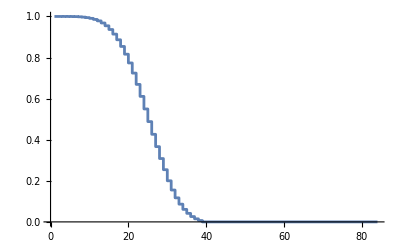

```mathematica
ListStepPlot[Table[bustOdds[bustCards[drawFour,n]],{n,2,84}]]
```

```mathematica
Table[n,{n,2,22}]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

```mathematica
drawSeven = drawCards[myDeck, 7];
```

```mathematica
bustOdds [list_]:=N[Count[list,-∞]/Length[list]]
```

```mathematica
bustOdds[drawSeven]
```

0.999088

```mathematica
N[399/400]
```

0.9975

Odds of busting on 21 with 7 drawn cards is 0.999088, or about 1/1000. For comparison, odds of NOT getting 20&20 with a disadvantaged roll is 0.9975.

## What about when you start to hit?

If you score less than a 12 on your first two cards, you should automatically hit, as it is impossible to bust. This needs to be taken into account, as what we really want is an odds table for the game state where the player has some chance of failing.

```mathematica
drawCards[myDeck,3]
```

```mathematica
Tuples/@Subsets[myDeck,{2}]
```

```mathematica
threeCards =MapIndexed[myDeck[[#]]&, Permutations[Range[52],{3}],{2}]
```

```mathematica
threeCards[[All,;;2]]
```

```mathematica
Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]])
```

```mathematica
Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}]
```

```mathematica
Tuples/@Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}]
```

```mathematica
Total[#,{2}]&/@(Tuples/@Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}])
```

```mathematica
finalTotal = bustCards[Total[#,{2}]&/@(Tuples/@Transpose[{Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]),threeCards[[All,3]]}]),21];
```

```mathematica
firstTwoTotal = bustCards[Total[#,{2}]&/@(Tuples/@threeCards[[All,;;2]]), 21];
```

```mathematica
thirdAtN = Pick[finalTotal,Map[#==20&,firstTwoTotal]]
```

```mathematica
Tally[Pick[threeCards[[All, ;;2]],Map[#==20&,firstTwoTotal]]]
```

{{{{1,11},{9}},800},{{{9},{1,11}},800},{{{10},{10}},12000}}

```mathematica
(12000*(50-4))/((12000+800+800)*50)
```

69/85

```mathematica
N[69/85]
```

0.811765

```mathematica
N[46/50]
```

0.92

This is a very interesting result! If you have a total of 20, and you hit, you only have an 81% chance of busting. Online tables show 92% odds, which at a glance seems more reasonable. What gives? Well, if you have A/9 combo, you have 20 but will never bust on the next turn (There are 1600 permutations of this). If you have any 10/10 combo (12,000 permutations of this), you will bust if your next card isn’t A. You drew two cards already, so 50 remain in the deck. 

Consider the 10/10. What are your odds of busting? Well, 46/50! That is our 92% from the internet. And we already know you have 0% odds from A/9.

```mathematica
1600/(12000+1600)*0+12000/(12000+1600)*0.92
```

0.811765

```mathematica
1600/(12000+1600)
```

2/17

```mathematica
N[2/17]
```

0.117647

```mathematica
N[2/17]
```

0.117647

```mathematica
N[2/15]
```

0.133333

How many Ace & 9 Combinations?

```mathematica
Binomial[13,1]*Binomial[12,1]*Binomial[4,1]*Binomial[4,1]
```

2496

How many 10 & 10 combinations?

```mathematica
Binomial[13,4]Binomial[]
```

```mathematica
Binomial[13,1]
```

13

```mathematica
Binomial[4,4]
```

1

```mathematica
13*13
```

169

```mathematica
N[Mean[thirdAtN]]
```

-∞

```mathematica
N[25/2]
```

12.5

```mathematica
N[Count[thirdAtN,x_/;x<0]/Length[thirdAtN]]
```

0.811765

```mathematica
N[27/80]
```

0.3375

```mathematica
N[228/775]
```

0.294194

```mathematica
critFail[thirdAtN,0,21]
```

Select::normal: Nonatomic expression expected at position 1 in Select[14,#1≤21&].

Select::normal: Nonatomic expression expected at position 1 in Select[15,#1≤21&].

Select::normal: Nonatomic expression expected at position 1 in Select[16,#1≤21&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

228/775

```mathematica
Length[Pick[finalTotal,Map[#==12&,firstTwoTotal]]]
```

12400

```mathematica
Tuples[{{"A"},{1, 2}}]
```

{{A,1},{A,2}}

```mathematica
Join[Subsets[myDeck,{1}]
```

{{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}},{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}},{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}},{{1,11}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{10}},{{10}},{{10}}}

```mathematica
Length[drawFive]
```

2598960

```mathematica
Count[drawFive,-∞]
```

2458988

```mathematica
Subsets
```

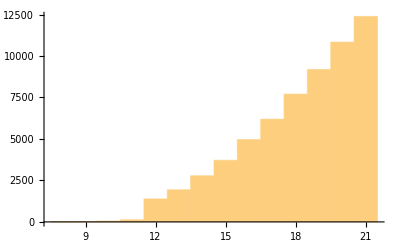

```mathematica
Histogram[drawCards[myDeck, 4]]
```

```mathematica
DeleteElements[myDeck,1->{{1, 11}, {1, 11}}]
```

{{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10},{1,11},{2},{3},{4},{5},{6},{7},{8},{9},{10},{10},{10},{10}}

```mathematica
drawTwo
```

{{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{2,12,12,22},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{3,13},{4},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{4,14},{5},{6},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{5,15},{6},{7},{8},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{6,16},{7},{8},{9},{10},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{7,17},{8},{9},{10},{11},{12},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{8,18},{9},{10},{11},{12},{13},{14},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{9,19},{10},{11},{12},{13},{14},{15},{16},{17},{18},{18},{18},{18},{19},{19},{19},{19},{10,20},{11},{12},{13},{14},{15},{16},{17},{18},{19},{19},{19},{19},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{11,21},{12},{13},{14},{15},{16},{17},{18},{19},{20},{20},{20},{20},{3,13},{4,14},{5,15},{6,16},{7,17},{8,18},{9,19},{10,20},{11,21},{11,21},{11,21},{11,21},{5},{6},{7},{8},{9},{10},{11},{12},{12},{12},{12},{7},{8},{9},{10},{11},{12},{13},{13},{13},{13},{9},{10},{11},{12},{13},{14},{14},{14},{14},{11},{12},{13},{14},{15},{15},{15},{15},{13},{14},{15},{16},{16},{16},{16},{15},{16},{17},{17},{17},{17},{17},{18},{18},{18},{18},{19},{19},{19},{19},{20},{20},{20},{20},{20},{20}}

```mathematica
Tuples[suit]
```

Tuples::normal: Nonatomic expression expected at position {1,1} in Tuples[{A,2,3,4,5,6,7,8,9,10,«3»}].

```mathematica
Tuples[Tuples[deck,2]]
```

Tuples::toomany: The length of the output of Tuples[{{{1,11},{1,11}},{{1,11},{2}},{{1,11},{3}},{{1,11},{4}},{{1,11},{5}},{{1,11},{6}},{{1,11},{7}},{{1,11},{8}},{{1,11},{9}},{{1,11},{10}},«2694»}] should be a machine integer.

```mathematica
Total[{{1, 11},{1,11}, 10}]
```

{12,32}

```mathematica
Tuples[{{1,11},{10}}]
```

{{1,10},{11,10}}

```mathematica
List[10]
```

{10}